```mathematica
ClearAll["Global`*"]
(*Last Update: 11/06/2020*)
(*AndreHAM*)
```

Particle in a box

#### Potential box -

```mathematica
(* Let`s "simulate" a potential box: the heaviside function will do the job *)

V[x_,height_,width_]:=height(HeavisideTheta[-x]+HeavisideTheta[x-width]) 

Manipulate[Plot[V[x,height,width],{x,-10,20},PlotRange->{-1,10},Filling->Axis],{height,0.1,10},{width,0.1,10}]
```

#### 1D - Wave function -

```mathematica
ℏ=6.6 10^-34; (* Planck Cte *)
m=9.1×10^−31; (* electron mass *)
L=10; (* width *)


Φ[n_,x_]:=√(2/L)Sin[(n π)/L x];  (* Wave function!  *)
Energy[n_]:= n^2(π^2 ℏ^2)/(2 m  L^2) (* Energy to the nth state *)

Prob[n_,x_]:=Abs[Φ[n,x]]^2; (* Probability of finding a particle in the state n at position x *)
```

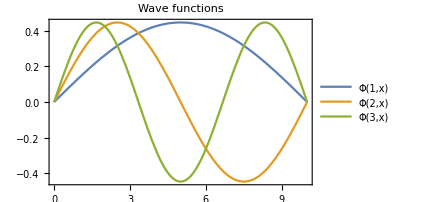

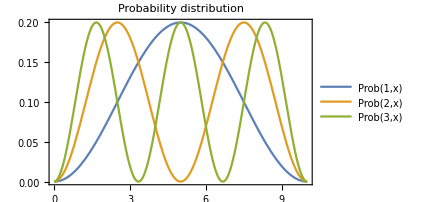

```mathematica
Plot[{Φ[1,x],Φ[2,x],Φ[3,x]},{x,0,L},PlotLegends->"Expressions",PlotLabel->"Wave functions"]
Plot[{Prob[1,x],Prob[2,x],Prob[3,x]},{x,0,L},PlotLegends->"Expressions",PlotLabel->"Probability distribution"]
```

#### Examples of a 1D superposition state -

```mathematica
(* Any normalized linear combination of the Φ[n,x] is a possible physical state *)


(* Check the normalization: Integrate[Abs[]^2,{x,0,L}]*)
Psi1[x_]:=√(1/2)(Φ[1,x]+Φ[2,x])
Psi2[x_]:=√(1/4)Φ[1,x]+√(1/4)Φ[2,x]+√(2/4)Φ[5,x]


Prob1[x_]:=Abs[Psi1[x]]^2; 
Prob2[x_]:=Abs[Psi2[x]]^2;
```

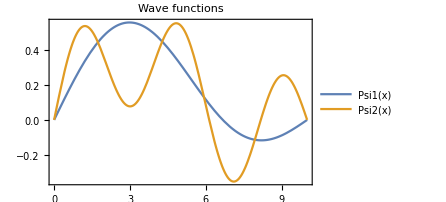

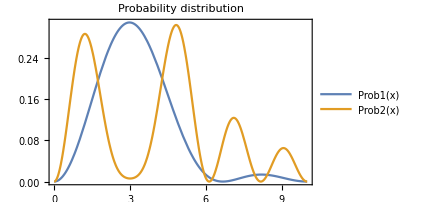

```mathematica
Plot[{Psi1[x],Psi2[x]},{x,0,L},PlotLegends->"Expressions",PlotLabel->"Wave functions"]
Plot[{Prob1[x],Prob2[x]},{x,0,L},PlotLegends->"Expressions",PlotLabel->"Probability distribution"]
```

#### 2D - Wave function -

```mathematica
Lx=10;
Ly=5;


Φx[n_,x_]:=√(2/L)Sin[(n π)/Lx x];  (* x - Wave function!  *)
Φy[n_,y_]:=√(2/L)Sin[(n π)/Ly y];  (* y - Wave function!  *)
```

```mathematica
Plot3D[{Φx[4,x]Φy[7,y]},{x,0,Lx},{y,0,Ly},PlotLegends->"Expressions",PlotLabel->"2D Wave function",Mesh->None]
```

-Graphics3D-